```mathematica
fsz=22;16;
(*path=NotebookDirectory[]<>"figures/"*)
fontFamilyPB="Latin Modern Math";"Helvetica";
fontFamily="Times New Roman";FontSize->24;

SetOptions[Plot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLinearPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[ListLogLogPlot,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];
SetOptions[Graphics,BaseStyle->{FontFamily->fontFamily,FontSize->fsz}];


lineStyle=Dashing[{1,0}];Automatic;xRPlotMin=0;ar=1;gridLines=Automatic;imSz=400;
pltStl={{lineStyle,Blue,Thickness[thickness=.013/2]},{lineStyle,RGBColor[0.7,0.3,0.0],Thickness[thickness]},{lineStyle,RGBColor[0.9,0.5,0.6],Thickness[thickness]},{lineStyle,Brown,Thickness[thickness]},{lineStyle,Black,Thickness[thickness]}};
```

```mathematica
Clear[F,B,O2,B0,C0,Func,M];
```

```mathematica
Func:=Module[{f,g,eqs,BC,DEq,sol},
f=HeavisideTheta[R[t]-R0]α A[t](R[t]-R0);
g=ϵ A[t]R[t]HeavisideTheta[R1-R[t]]+ϵ A[t] R1 HeavisideTheta[R[t]-R1];

eqs={R'[t] == -f-g-ξ ω R[t] G[t]+σ1,
G'[t]== ((1-ξ)ω R[t] - a1) G[t],
H'[t]==  ((1-ψ)Ω CH[t] - a2) H[t],
L'[t]== f - β B[t] L[t]+ξ ω R[t] G[t],
CO'[t]==μ O2[t] g + γ λ O2[t] CH[t] F[t]+ψ Ω CH[t] H[t],
CH'[t] == κ β B[t] L[t] - γ O2[t] CH[t] F[t],
O2'[t] == -(μ O2[t] g + γ λ O2[t] CH[t] F[t])+σ2,
A'[t] == (1-μ)O2[t]g - s A[t],
B'[t]==((1-κ) β L[t] -u) B[t],
F'[t] == ((1-λ)γ O2[t] CH[t]-ν)F[t]};
BC = {R[0]==RI,L[0]==0,CO[0]==0,CH[0]==0,A[0]==A0,B[0]==B0,F[0]==C0,O2[0]==O20,G[0]==G0,H[0]==H0};
DEq = Flatten[{eqs,BC}];

sol=NDSolve[DEq,{A,B,F,O2',CH',L',CO',R',O2,CH,L,CO,R,G,H},{t,0,Tmax},PrecisionGoal->10];
First[sol]
(*{Plot[Evaluate[{F[t],B[t],A[t]}/.sol],{t,0,Tmax},PlotRange->PR,PlotLegends->{"F","B","A"}],
Plot[Evaluate[{O2'[t],CH'[t],L'[t],CO'[t],R'[t]}/.sol],{t,0,Tmax},PlotRange->All,PlotLegends->{"O2","CH4","Lac","CO2","R"}],
Plot[Evaluate[{O2[t],CH[t],L[t],CO[t],R[t]}/.sol],{t,0,Tmax},PlotRange->All,PlotLegends->{"O2","CH4","Lac","CO2","R"}]
};*)
]
```

```mathematica
R0=2.5;
R1=1;

a2 = 0.5;
a1=0.5; (* 0.1  *)
s=0.1;
ν=0.1;
u=0.1;

λ=0.5; 
κ=0.5;
μ=0.5;
ξ=0.5; (* 0.5 *)
ψ=0.5;

A0=1.;
H0=1; (*1? *)
G0=1;
B0=1;
C0=1;

β=0.5; 
α=0.5; (* 0.5 *)
ω=0.02; (* 0.02 *)
Ω=0.02;
ϵ=0.5;
γ=0.5;
```

#### Oscillation qualitative analysis

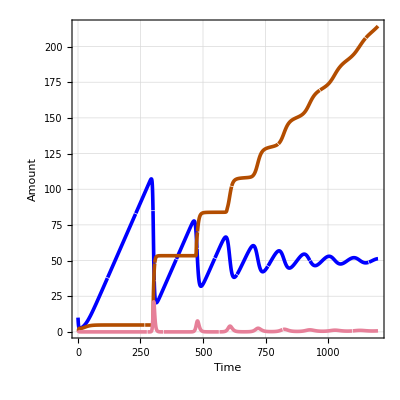

```mathematica
RI=10;
O20=1;
σ1 = 0.4; (* resource rate  0 for oxygen impulse only *)
σ2 = 0; (* oxygen rate 0 for resource impulse only *)
Tmax =1200;
sol  = Func;
tx = 97;

Quiet@Plot[Evaluate[{R[t],CH[t],G[t]}/.sol],{t,0,Tmax}(*,PlotRange->All*),(*PlotLegends->Placed[{"g GL_ij","g (H-ω)^-1","ψ_j"},{.65,.5}],*)PlotRange->All,AspectRatio->1,(*ImageSize->250,*)FrameLabel->{"Time","Amount"},
PlotLegends->Placed[LineLegend[{Style["R",FontSize->fsz,FontFamily->fontFamily],Style["CH_4",FontSize->fsz,FontFamily->fontFamily],Style["F",FontSize->fsz,FontFamily->fontFamily]},Spacings-> 0.2],{0.25,0.77}],ImageSize->imSz,Axes->None,PlotStyle->pltStl,Frame->True,BaseStyle->{FontFamily->"Times New Roman",FontSize->fsz},FrameStyle->Thick,FrameTicksStyle->Black,LabelStyle->Black,GridLines->gridLines,AspectRatio->ar
]
```

```mathematica
txx=80;
G'[txx]/.sol
```

-1.90146×10^-12

InterpolatingFunction::dmval: Input value {580} lies outside the range of data in the interpolating function. Extrapolation will be used.

4.01359×10^-10

```mathematica
B[txx]/.sol
```

0.606025

```mathematica
Rt0=10;
xs = a1-(1-ξ)ω Rt0;
ϵ0=10^(-20);
```

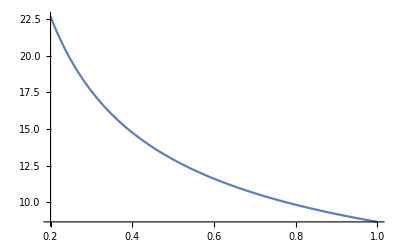

```mathematica
Plot[(xs+√(xs^2-2(1-ξ)ω Rt0 σ Log[ϵ0]))/(xs σ),{σ,0.2,1}]
```